```mathematica
/Users/warren/Documents/Princeton/EGR191/Lab 7/Mathematica Code
```

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==-u Log[(M2/M1)]-gt,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→-0.199024+33.7402 t-1. gt t}}

-0.199024+33.7402 t-1. gt t

-0.199024 t+16.8701 t^2-0.5 gt t^2

33.7402-1. gt

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

```mathematica
sol2=DSolve[{v'[t]==-u Log[((M1-M0t)/M1)]-gt,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→-0.199024-1. gt t-26.0768 t Log[1.45159 (0.6889-1. M0t)]}}

-0.199024-1. gt t-26.0768 t Log[1.45159 (0.6889-1. M0t)]

-0.199024 t-0.5 gt t^2-13.0384 t^2 Log[1.45159 (0.6889-1. M0t)]

-1. gt-26.0768 Log[1.45159 (0.6889-1. M0t)]

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==-u Log[((M1-M0*t)/M1)]-gt,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→-0.199024+26.0768 t-1. gt t+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]}}

-0.199024+26.0768 t-1. gt t+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]

-5.0585 t+19.5576 t^2-0.5 gt t^2-1.81115 Log[1.-2.68309 t]+9.71894 t Log[1.-2.68309 t]-13.0384 t^2 Log[1.-2.68309 t]

26.0768-1. gt-26.0768/(1.-2.68309 t)+(69.9664 t)/(1.-2.68309 t)-26.0768 Log[1.-2.68309 t]

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

{{v[t]→-0.199024+26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]}}

-0.199024+26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]

-5.0585 t+19.5576 t^2-1.635 t^3-1.81115 Log[1.-2.68309 t]+9.71894 t Log[1.-2.68309 t]-13.0384 t^2 Log[1.-2.68309 t]

26.0768-26.0768/(1.-2.68309 t)-9.81 t+(69.9664 t)/(1.-2.68309 t)-26.0768 Log[1.-2.68309 t]

26.0768

0.1889

0.6889

1.84838

9.81

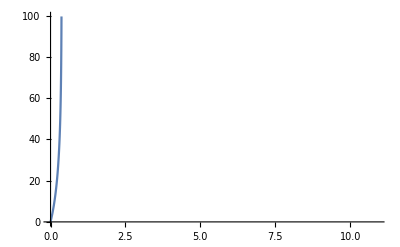

```mathematica
sol2=DSolve[{v'[t]==-u*Log[((M1-M0*t)/M1)]-g*t,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==-u*Log[((M1-M0*t)/M1)]-g*t,v[0]==0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]}}

26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]

-4.85947 t+19.5576 t^2-1.635 t^3-1.81115 Log[1.-2.68309 t]+9.71894 t Log[1.-2.68309 t]-13.0384 t^2 Log[1.-2.68309 t]

26.0768-26.0768/(1.-2.68309 t)-9.81 t+(69.9664 t)/(1.-2.68309 t)-26.0768 Log[1.-2.68309 t]

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

DSolve[{v'[t]==9.81-5.29381 C k v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0})

{{v[t]→(-g M1 t+A1 P1 t)/M1}}

(-g M1 t+A1 P1 t)/M1

-(g t^2)/2+(A1 P1 t^2)/(2 M1)

(-g M1+A1 P1)/M1

340000.

0.0000708822

0.6889

9.81

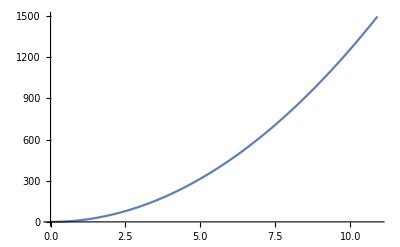

```mathematica
Clear[P1,A1,M1,g,u,M0]

sol1=DSolve[{v'[t]==(P1*A1)/M1-g,v[0]==0},v[t],t]
vsol1[t_]=v[t]/.sol1[[1]]
h1[t_]=Integrate[vsol1[t],t]
a1[t_]=D[vsol1[t],t]

P1=3.4*10^5
A1=((4.75*10^(-3))^2)*Pi
M1=0.6889
g=9.81

Plot[h1[t],{t,0,10.91}]
```

{{v[t]→-1/M04.905 (1. M0 t^2-0.203874 M0 t u-0.140449 u Log[1.-1.45159 M0 t]+0.203874 M0 t u Log[1.-1.45159 M0 t])}}

-1/M04.905 (1. M0 t^2-0.203874 M0 t u-0.140449 u Log[1.-1.45159 M0 t]+0.203874 M0 t u Log[1.-1.45159 M0 t])

-1.635 t^3-(0.34445 t u)/M0+0.75 t^2 u-(0.237292 u Log[1.-1.45159 M0 t])/M0^2+(0.6889 t u Log[1.-1.45159 M0 t])/M0-0.5 t^2 u Log[1.-1.45159 M0 t]

-1/M04.905 (2. M0 t-0.203874 M0 u+(0.203874 M0 u)/(1.-1.45159 M0 t)-(0.295941 M0^2 t u)/(1.-1.45159 M0 t)+0.203874 M0 u Log[1.-1.45159 M0 t])

26.0768

0.1889

0.6889

1.84838

9.81

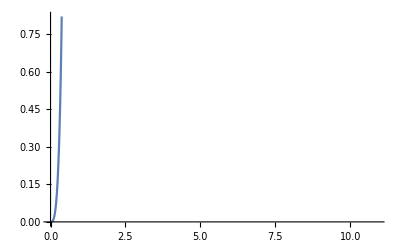

```mathematica
sol2=DSolve[{v'[t]==-u*Log[((M1-M0*t)/M1)]-g*t,v[0]==0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[h2[t],{t,0,10.91}]
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

k=ρ2*A2/2
C=0.1
A2=((.06)^2)*Pi

Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

DSolve[{v'[t]==9.81-5.29381 C k v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.81-5.29381 C k v^2,v[0]==0})

0.00689894

0.1

0.0113097

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2]},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
```

NDSolve[{V'[t]==0.0130371 pi √(-100000+2 P0 (V0/V[t])^9.81)},V[t],{t,0,1}]

340000.

0

1000

9.81

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2]},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
```

NDSolve[{V'[t]==0.375506 pi √((V0/V[t])^9.81)},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2]},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==0.00184838 √((V0/V[t])^9.81)},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2]},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==2.60327×10^-17 √((1/V[t])^9.81)},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2],V[0]==0},v[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==2.60327×10^-17 √((1/V[t])^9.81),V[0]==0},v[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2],V[0]==0},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
0.0015
```

NDSolve[{V'[t]==2.60327×10^-17 √((1/V[t])^9.81),V[0]==0},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

0.0015

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2],V[0]==0},V[t],{t,0,1}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==2.60327×10^-17 √((1/V[t])^9.81),V[0]==0},V[t],{t,0,1}]

340000.

0

1000

9.81

0.0000708822

0.0015

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g)-P2)/ρ2],V[0]==0},V[t],{t,1,4}]
P0=3.4*10^5
P2=0
ρ2=1000
g=9.81
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==2.60327×10^-17 √((1/V[t])^9.81),V[0]==0},V[t],{t,1,4}]

340000.

0

1000

9.81

0.0000708822

0.0015

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(gamma)-P2)/ρ2],V[0]==0},V[t],{t,0,4}]
P0=3.4*10^5
P2=0
ρ2=1000
gamma=5/7
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==0.00184838 √(0.0015^gamma (1/V[t])^gamma),V[0]==0},V[t],{t,0,4}]

340000.

0

1000

5/7

0.0000708822

0.0015

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g1)-P2)/ρ2],V[0]==0},V[t],{t,0,4}]
P0=3.4*10^5
P2=0
ρ2=1000
g1=5/7
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==0.00184838 √(0.0015^g1 (1/V[t])^g1),V[0]==0},V[t],{t,0,4}]

340000.

0

1000

5/7

0.0000708822

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=NDSolve[{V'[t]==A*Sqrt[(2*P0(V0/V[t])^(g1)-P2)/ρ2],V[0]==0},V[t],{t,0,4}]
P0=3.4*10^5
P2=0
ρ2=1000
g1=5/7
A=((4.75*10^(-3))^2)*Pi
V0=0.0015
```

NDSolve[{V'[t]==0.000181239 (1/V[t])^(5/14),V[0]==0},V[t],{t,0,4}]

340000.

0

1000

5/7

0.0000708822

0.0015

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==(2*A(P1-P2))/(M-ρ1*ve*A*t),v[0]==0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

P1=3.4*10^5
P2=0
ve=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81
ρ1=1000
A=((4.75*10^(-3))^2)*Pi
```

{{v[t]→(680. (1. Log[1. M]-1. Log[1. M-0.0708822 t ve]))/ve}}

(680. (1. Log[1. M]-1. Log[1. M-0.0708822 t ve]))/ve

(680. t)/ve+(680. t Log[M])/ve+(9593.38 M Log[1. M-0.0708822 t ve])/ve^2-(680. t Log[1. M-0.0708822 t ve])/ve

48.1999/(1. M-0.0708822 t ve)

340000.

0

26.0768

0.1889

0.6889

1.84838

9.81

1000

0.0000708822

```mathematica
Plot[h2[t],{t,0,10.91}]
Plot[vsol2[t],{t,0,10.91}]
Plot[a2[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ClearAll
```

ClearAll

{{v[t]→-3.39279×10^-7-26.0768 Log[1.-1. t]}}

-3.39279×10^-7-26.0768 Log[1.-1. t]

26.0768 t+26.0768 Log[1.-1. t]-26.0768 t Log[1.-1. t]

26.0768/(1.-1. t)

340000.

0

26.0768

0.1889

0.6889

1.84838

9.81

1000

0.0000708822

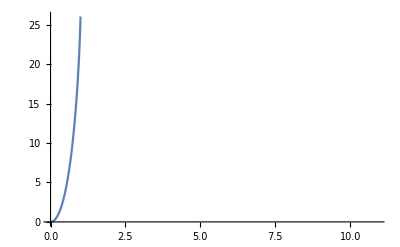

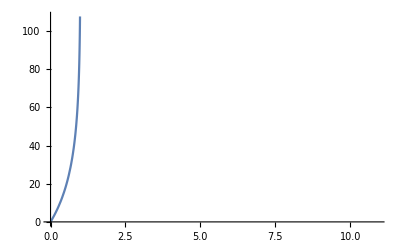

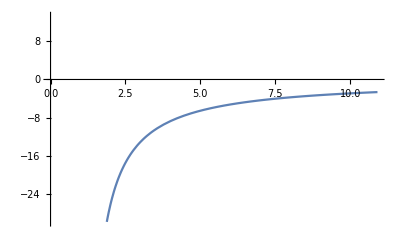

```mathematica
sol2=DSolve[{v'[t]==(2*A(P1-P2))/(M0-ρ1*ve*A*t),v[0]==0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

P1=3.4*10^5
P2=0
ve=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81
ρ1=1000
A=((4.75*10^(-3))^2)*Pi

Plot[h2[t],{t,0,10.91}]
Plot[vsol2[t],{t,0,10.91}]
Plot[a2[t],{t,0,10.91}]
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
ve=26.07680962
```

DSolve[{v'[t]==9.81-0.0365216 C v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
v=26.07680962
```

DSolve[{v'[t]==9.81-0.0365216 C v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.81-0.0365216 C v^2,v[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
ClearAll
```

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
v=26.07680962
```

DSolve[{0==9.81-24.8347 C,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

```mathematica
ClearAll
```

ClearAll

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*v1^2)/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
v1=26.07680962
```

DSolve[{0==9.81-0.0365216 C v1^2,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-0.0365216 C v1^2,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-0.0365216 C v1^2,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-0.0365216 C v1^2,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
ClearAll
```

ClearAll

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
ve=26.07680962
```

DSolve[{0==9.81-24.8347 C,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
sol3=DSolve[{v'[t]==g-(k*(C)*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M2=.1889
ve=26.07680962
```

DSolve[{0==9.81-24.8347 C,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol3=DSolve[{v'[t]==g-(k*(C)*(ve)^(2))/(M_2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.1
M_2=.1889
ve=26.07680962
```

DSolve[{0==9.81-(2.34564 C)/M_,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-(2.34564 C)/M_,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-(2.34564 C)/M_,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-(2.34564 C)/M_,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.1

0.1889

26.0768

```mathematica
ClearAll
```

ClearAll

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.5
M2=.1889
ve=26.07680962

Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

DSolve[{0==9.81-24.8347 C,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 C,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.5

0.1889

```mathematica
C
```

C

```mathematica
C
```

C

```mathematica
C = 0.1
```

0.1

```mathematica
C
```

C

```mathematica
sol3=DSolve[{v'[t]==g-(k*x*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
x=0.5
M2=.1889
ve=26.07680962

Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

DSolve[{0==9.81-24.8347 x,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{0==9.81-24.8347 x,26.0768[0]==0}

∫(26.0768[t]/.{0==9.81-24.8347 x,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{0==9.81-24.8347 x,26.0768[0]==0})

1.22

0.0113097

0.00689894

0.5

0.1889

26.0768

-Graphics-

-Graphics-

-Graphics-

```mathematica
C =
```

```mathematica
ve
```

26.0768

```mathematica
x
```

0.5

```mathematica
sol3=DSolve[{v'[t]==g-(k*x*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

DSolve[{False,26.0768[0]==0},26.0768[t],t]

26.0768[t]/.{False,26.0768[0]==0}

∫(26.0768[t]/.{False,26.0768[0]==0})ⅆt

∂_t (26.0768[t]/.{False,26.0768[0]==0})

```mathematica
ClearAll
```

ClearAll

```mathematica
ve
```

26.0768

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ve
```

26.0768

```mathematica
v
```

26.0768

```mathematica
Clear["Global`*"]
```

```mathematica
v
```

v

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]

g=9.8
ρ2=1.22
A2=((.06)^2)*Pi
k=ρ2*A2/2
C=0.5
M2=.1889
ve=26.07680962
```

{{v[t]→(g M2 t-C k t ve^2)/M2}}

(g M2 t-C k t ve^2)/M2

1/2 t^2 (g-(C k ve^2)/M2)

(g M2-C k ve^2)/M2

9.8

1.22

0.0113097

0.00689894

0.5

0.1889

26.0768

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol3=DSolve[{v'[t]==g-(k*C*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

{{v[t]→9.8 t-24.8347 C t}}

9.8 t-24.8347 C t

4.9 t^2-12.4174 C t^2

9.8-24.8347 C

```mathematica
c
```

c

```mathematica
C
```

C

```mathematica
C = 0.1
```

0.1

```mathematica
C
```

C

```mathematica
c = 1
```

1

```mathematica
c
```

1

```mathematica
c = .1
```

0.1

```mathematica
sol3=DSolve[{v'[t]==g-(k*c*(ve)^(2))/(M2),v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

{{v[t]→7.31653 t}}

7.31653 t

3.65826 t^2

7.31653

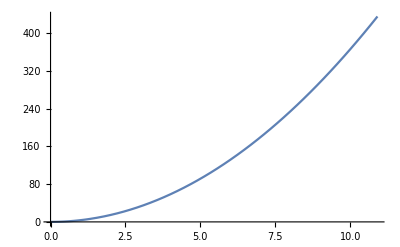

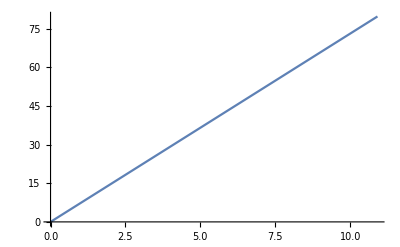

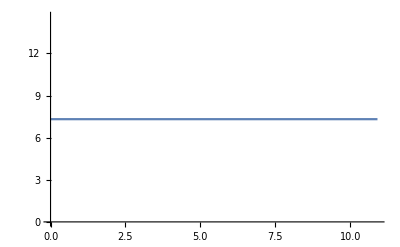

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

```mathematica
sol3=DSolve[{v'[t]==(k*c*(ve)^(2))/(M2)-g,v[0]==0},v[t],t]
vsol3[t_]=v[t]/.sol3[[1]]
h3[t_]=Integrate[vsol3[t],t]
a3[t_]=D[vsol3[t],t]
```

{{v[t]→-7.31653 t}}

-7.31653 t

-3.65826 t^2

-7.31653

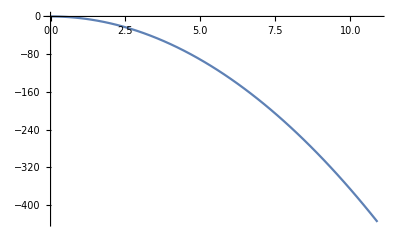

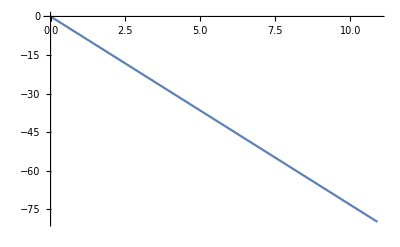

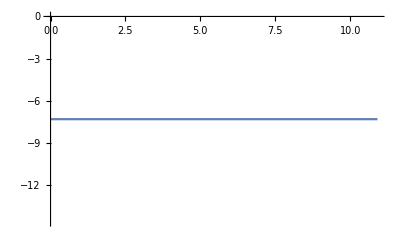

```mathematica
Plot[h3[t],{t,0,10.91}]
Plot[vsol3[t],{t,0,10.91}]
Plot[a3[t],{t,0,10.91}]
```

```mathematica
sol4=DSolve[{v'[t]==g+(k*c*v^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

DSolve[{v'[t]==9.8+0.00365216 v^2,v[0]==0},v[t],t]

v[t]/.{v'[t]==9.8+0.00365216 v^2,v[0]==0}

∫(v[t]/.{v'[t]==9.8+0.00365216 v^2,v[0]==0})ⅆt

∂_t (v[t]/.{v'[t]==9.8+0.00365216 v^2,v[0]==0})

```mathematica
sol4=DSolve[{v'[t]==g+(k*c*(ve)^2)/(M2),v[0]==0},v[t],t]
vsol4[t_]=v[t]/.sol4[[1]]
h4[t_]=Integrate[vsol4[t],t]
a4[t_]=D[vsol4[t],t]
```

{{v[t]→12.2835 t}}

12.2835 t

6.14174 t^2

12.2835